## Auxiliary functions

```mathematica
fidelityXY[M_]:=(
Utarget = Cos[θ]*σX + Sin[θ]*σY;
NMaximize[Abs[fidelity2D[Utarget, M]], {θ}][[1]]
)

XYangle[M_] := (
Utarget = Cos[θ]*σX + Sin[θ]*σY;
θ /. NMaximize[Abs[fidelity2D[Utarget, M]], {θ}][[2]]
)

Clear[fidelityToGate];
fidelityToGate[Ea_?NumericQ, Ba_?NumericQ, ωEin_?NumericQ, ωBin_?NumericQ,gate_] := (

Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/5, T2];
ωE = ωEin;
ωB = ωBin;

U = findEvolutionOperator2D[Hcorrected, Tmax];

If[gate == "XY",
F = fidelityXY[U /. t->Tmax],
F = fidelity2D[gate, U /. t->Tmax] // Chop
]

Print[{F, {ΔE, B0,Vt, Ea, Ba, ωEin, ωBin, Tmax}}];

output = F;

If[output > bestSoFar, (
bestSoFar = output;
bestParameters = {ΔE, B0,Vt, Ea, Ba, ωEin, ωBin, Tmax};
)];

Pause[1];

output
)


Clear[map]
map[x_, a_, b_] := a + (b - a)*x // Re
```

## Optimize Gate

0.999879

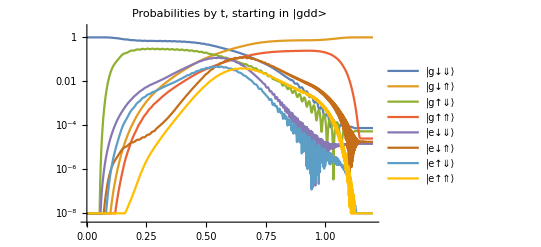

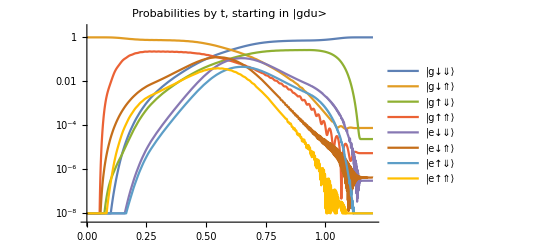

----------------------------------------startin'----------------------------------------

BOUNDS: Ea {122.,366.} --- Ba {0.0159,0.0477} --- ωE: {3.35674×10^10,3.39674×10^10} --- ωB: {3.34582×10^10,3.38582×10^10}

$Aborted

```mathematica
clearVariables[]
setVariables[]

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;
Δ = 2000;
ϵ0Mid = ϵ0 /. ΔE->ΔEMid;

EaD =244;
ωED = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 1*2*π*2.0548*10^8 /. ΔE->ΔEMid;
ωED = 3.3767399946666843*^10;

(*BaD =EaD*(d*e)/(γe*h);*)
BaD = .0318;
ωBD = 2*π*(B0*γe - A*dState[[1]]^2/2) - 1*2*π*1.9759*10^8 /. ΔE->ΔEMid;
ωBD = 3.365817946982966*^10;

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12];

(*fidelityToGate[EaD, BaD, ωED, ωBD, "XY"]*)
Clear[Eamp, Bamp];
Eamp[t_] := EaD*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := BaD*cosWindow[t - T1, T2/5, T2];
ωE = ωED;
ωB = ωBD;

U = findEvolutionOperator2D[Hcorrected, Tmax];
(*U = (Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];
Uuncut = U;*)

fidelityXY[U[[{1, 2}, {1, 2}]] /. t->Tmax]

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]



Print["----------------------------------------" <> "startin'" <> "----------------------------------------"];
TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

δ = 2;
γ = .5;

Print["BOUNDS: Ea " <> ToString[{EaD*(1 - γ), EaD*(1 + γ)}, TraditionalForm] <> " --- Ba " <> ToString[{BaD*(1 - γ), BaD*(1 + γ)}, TraditionalForm] <> " --- ωE: " <> ToString[{ωED - δ*10^8, ωED + δ*10^8}, TraditionalForm] <> " --- ωB: " <> ToString[{ωBD - δ*10^8, ωBD + δ*10^8}, TraditionalForm]]
NMaximize[
{
fidelityToGate[
map[x1, EaD*(1 - γ), EaD*(1 + γ)],
 map[x1, BaD*(1 - γ), BaD*(1 + γ)],
map[x3, ωED - δ*10^8, ωED + δ*10^8],
map[x4, ωBD - δ*10^8, ωBD + δ*10^8],
"XY"],
0 < x1 < 1,
0 < x2 < 1,
0 < x3 < 1,
0 < x4 < 1
},
{{x1,.3, .7}, {x2, .3, .7}, {x3, .3, .7}, {x4,.3, .7}(*, {x5,.3, .7}, {x6,.3, .7}, {x7,.3, .7}, {x8,.3, .7}, {x9,.3, .7}*)},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]



clearVariables[]
```

```mathematica
{0.9999793195771143,{-2000+(40000000000 Re[t])/3,0.2,5.597446*^9,116.6811850892453,0.015130524804322143,3.3878701996967476*^10,3.3722858986273052*^10,3/10000000}}
```

{0.999979,{-2000+(40000000000 Re[t])/3,0.2,5.59745×10^9,116.681,0.0151305,3.38787×10^10,3.37229×10^10,3/10000000}}

## Generate Spectrum of X-Rotations

```mathematica
setVariables[]

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;
ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12];
ϵ0Mid = ϵ0 /. ΔE->ΔEMid;


Ea =244;
ωE = 3.3767399946666843*^10;

Ba = .0318;
ωB = 3.365817946982966*^10;

Eamp[t_] := Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/5, T2];
(*Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t - T1, T2/10, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/10, T2];

U = findEvolutionOperator2D[Hcorrected, Tmax];
(*U = (Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];
Uuncut = U;*)

fidelityXY[U[[{1, 2}, {1, 2}]] /. t->Tmax]
ϕ = XYangle[U[[{1, 2}, {1, 2}]] /. t->Tmax];*)

Ubase = MatrixExp[-ⅈ*t*(HcorrectedStatic /. t->0) // N];

ϕX[λ_] := (
Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/5, T2];

statusString="λ = " <> ToString[λ] <> "          ";
findEvolutionOperator2D[Hcorrected, Tmax];
U = (ConjugateTranspose[Ubase].Uuncut)[[{1, 2}, {1, 2}]];
UU = U /. t->Tmax;

gateDecompositionParameters[UU]
)

ϕs = {};
Do[AppendTo[ϕs, Join[{λ}, ϕX[λ]]], {λ, 0, 1, .1}];
ϕs

clearVariables[]
```

{{0.,0.63009,0.,0.63009,5.71562,1.},{0.02,0.306,0.00164304,0.963524,5.76156,1.},{0.04,0.311177,0.00657218,0.986339,5.89932,1.},{0.06,0.319781,0.0147874,1.02424,6.12875,1.},{0.08,0.33178,0.0262883,1.07706,0.166425,1.},{0.1,0.347126,0.0410743,1.14455,0.578352,1.},{0.12,0.365764,0.0591437,1.22638,1.0809,1.},{0.14,0.387625,0.0804935,1.3222,4.81513,0.999999},{0.16,0.412634,0.105119,1.43157,5.49723,0.999999},{0.18,0.440708,0.133013,1.554,6.26806,0.999999},{0.2,0.471761,0.164166,1.68895,0.843656,0.999999},{0.22,0.5057,0.198563,1.83585,4.9311,0.999999},{0.24,0.542431,0.236186,1.99409,5.96309,0.999998},{0.26,0.581861,0.27701,2.16301,0.797011,0.999999},{0.28,0.623894,0.321004,2.34194,5.13976,0.999999},{0.3,0.668433,0.368126,2.53022,0.140661,0.999998},{0.32,0.71538,0.418321,2.72714,1.5065,0.999998},{0.34,0.764638,0.471524,2.93201,6.09446,0.999998},{0.36,0.816107,0.527653,3.14416,1.33693,0.999998},{0.38,0.869679,0.586606,3.36291,6.08215,0.999999},{0.4,0.925248,0.64827,3.58763,1.47928,0.999997},{0.42,0.982699,0.712505,3.81768,0.0933178,0.999999},{0.44,1.04191,0.779167,4.05248,5.06452,0.999997},{0.46,1.10276,0.848085,4.29147,0.683536,1.},{0.48,1.16511,0.919097,4.53409,5.79855,0.999997},{0.5,1.22882,0.992019,4.77983,1.55861,0.999999},{0.52,1.29376,1.0667,5.02819,0.528706,0.999997},{0.54,1.35979,1.14296,5.27868,5.84904,0.999999},{0.56,1.42676,1.22068,5.53082,4.95185,0.999998},{0.58,1.49455,1.29974,5.78414,0.977364,0.999997},{0.6,1.56302,1.38004,6.03814,0.207397,0.999999},{0.62,1.63207,1.46153,0.00918674,5.78219,0.999997},{0.64,1.70159,1.54416,0.263148,5.13403,0.999997},{0.66,1.77151,1.62792,0.516388,1.40319,0.999999},{0.68,1.84175,1.7128,0.768441,0.871556,0.999996},{0.7,1.91228,1.79879,1.01886,0.396242,0.999996},{0.72,1.98308,1.88586,1.26725,6.25918,0.999998},{0.74,2.05413,1.97403,1.51323,5.89274,0.999996},{0.76,2.12543,2.06321,1.75645,5.5789,0.999994},{0.78,2.19702,2.15331,1.99663,5.31647,0.999995},{0.8,2.26892,2.24422,2.23355,5.10426,0.999996},{0.82,2.34116,2.33581,2.46698,4.94113,0.999994},{0.84,2.41374,2.42787,2.69673,4.82596,0.999992},{0.86,2.48668,2.52017,2.92268,4.75765,0.999993},{0.88,2.55996,2.61248,3.14468,4.73512,0.999994},{0.9,2.63342,2.70453,3.36248,4.75733,0.999993},{0.92,2.70669,2.79606,3.57563,4.82325,0.999992},{0.94,2.77879,2.88678,3.78308,4.93188,0.999992},{0.96,2.84647,2.97639,3.98152,5.08224,0.999992},{0.98,2.89146,3.0646,4.1526,5.2734,0.999992},{1.,0.359974,3.13055,1.74245,5.50442,0.999992}}

```mathematica
ϕs = {{0.,5.390828769701158,0.,5.390828769701158,0.9552540826724437,0.9999999972774982},{0.02,3.5442927887405924,0.001643043115562933,0.9635240583335326,1.0011918137840012,1.0000000185331697},{0.04,3.5494690919844194,0.00657217930979955,0.9863387229782129,1.1389542880574886,0.9999999899900847},{0.06,3.558073383739532,0.014787368015516014,1.024243732687002,1.3683896721880444,0.9999999423017286},{0.08,3.5700719287253904,0.02628834310505841,1.0770613209389674,4.8308387169882865,0.9999998726741064},{0.1,3.5854186289579157,0.04107433230091952,1.1445453473556289,5.242765856489714,0.9999997673710601},{0.12,3.6040561314023756,0.05914369313040554,1.226383971848621,5.745317479123111,0.9999996164816931},{0.14,3.6259171802457217,0.08049348016683337,1.3222029986236292,0.054768954619329284,0.9999994473835663},{0.16,3.6509261517207916,0.10511894726419369,1.4315697814448025,0.7368619813582986,0.9999993644008502},{0.18,3.6790006660361305,0.13301298925958965,1.5539976339100674,1.5076966652750006,0.9999994392792653},{0.2,3.710053114865254,0.1641655378939865,1.688951016014253,5.5080698961757815,0.9999994100396856},{0.22,3.7439920880331,0.1985627989676168,1.8358517694053664,0.17073921956621627,0.9999988500039685},{0.24,3.7807238578620432,0.236186072622928,1.994085199181821,1.2027249193343776,0.9999983471373067},{0.26,3.8201536956433686,0.2770104835073171,2.163005170935039,5.461424535300565,0.9999989061643745},{0.28,3.862186310221818,0.3210041464650468,2.341942761234257,0.3793970042480693,0.9999989501738833},{0.3,3.9067251788538924,0.3681255792296819,2.53021694871184,4.805074581402854,0.9999977903256646},{0.32,3.953672598309173,0.4183206571809301,2.7271359741573837,6.170912009078751,0.9999984670033752},{0.34,4.002930599926819,0.4715239988951825,2.932008234648639,1.3340972687758317,0.9999982601272985},{0.36,4.054398962847907,0.527652733247467,3.14415702856626,6.001338961538129,0.9999977501186913},{0.38,4.107971589606836,0.5866062509543635,3.362910035287257,1.3217893362891642,0.9999985988088336},{0.4,4.163540326061755,0.6482703805686514,3.5876261940438163,6.143688648312714,0.9999970449715222},{0.42,4.220991490396867,0.7125054716187871,3.8176821411907786,4.757731339028649,0.9999992516794063},{0.44,4.28020289632115,0.7791671004654096,4.0524838885021275,0.304152162325316,0.9999965660695312},{0.46,4.341049557803782,0.8480850388952287,4.291466692290712,5.3479492568974205,0.9999995271594498},{0.48,4.403398765469758,0.9190965066871579,4.534087153220521,1.0381836993802118,0.9999966632873855},{0.5,4.467113039921431,0.9920194631211133,4.779828418854604,6.223025029340477,0.999999475070477},{0.52,4.532054367494334,1.0666958312711992,5.028190211236938,5.193119962863145,0.9999971391305597},{0.54,4.598079234222439,1.1429592720484942,5.2786796658469095,1.0886725362602934,0.9999988394944623},{0.56,4.665053193145024,1.2206786281103974,5.530824633169894,0.1914872342090873,0.9999984269815045},{0.58,4.732837511062273,1.2997363101282695,5.784135269462908,5.64177766824235,0.9999973081518153},{0.6,4.801311670278405,1.380036863027341,6.038144631777875,4.871810630585305,0.9999994590483477},{0.62,4.8703601264816125,1.4615286018409,0.009186739853368486,1.02182508374582,0.9999973726529512},{0.64,4.939881047822697,1.5441622608459806,0.2631484127253887,0.37366529693117284,0.9999972308374201},{0.66,5.009798349652478,1.6279167983564597,0.5163883288365353,6.067605802584914,0.9999992109273748},{0.68,5.0800460637536045,1.7127977997500117,0.7684414574145326,5.53596971750249,0.9999964214148842},{0.7000000000000001,5.150574086517928,1.7987857535561398,1.0188590942004447,5.060655635980437,0.9999959123396455},{0.72,5.221368295682485,1.885864832814614,1.2672489596654184,1.4988108524501553,0.9999982356165714},{0.74,5.292420340962001,1.9740261111756958,1.5132314772027744,1.1323770269956857,0.9999959707069028},{0.76,5.363723744749309,2.0632060461886117,1.7564516021800674,0.8185388170262596,0.9999937953397071},{0.78,5.435308146762344,2.1533054058292294,1.9966347145948982,0.5561024567509958,0.9999954879807671},{0.8,5.507213278970416,2.2442230554612355,2.2335510875344577,0.34389634585083234,0.9999957980128481},{0.8200000000000001,5.579450579545659,2.3358137269145445,2.4669765863192223,0.18076994335634344,0.9999935253706674},{0.84,5.652030426355147,2.4278711713085532,2.6967294571443885,0.06559897271991913,0.9999921257663451},{0.86,5.724972734340004,2.5201689621008874,2.922679025798205,6.2804712981516495,0.9999930648836657},{0.88,5.798249714626279,2.6124754061483793,3.144678089735363,6.257943305622483,0.999993785937289},{0.9,5.871714183502002,2.704534617109135,3.3624815168156275,6.280150239382164,0.9999925908012601},{0.92,5.944986944452599,2.796064692997312,3.5756312748665033,0.06288222467929104,0.9999916330587346},{0.9400000000000001,6.017082939302299,2.886776987764628,3.7830762779157316,0.17151169474573438,0.999991766897143},{0.96,6.084766890935193,2.9763886345031914,3.981515626930287,0.32187922075181924,0.9999919226205201},{0.98,6.129757309473404,3.0645963189434493,4.152595679119089,0.5130347364610319,0.9999919978544166},{1.,3.59826678641764,3.1305485857799,1.7424451606044309,0.7440525895069539,0.9999919473473349}};
```

```mathematica
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)
Do[
ϕs[[All, i]] = unravel[ϕs[[All, i]]],
{i, {2, 4}}];
(*ϕs[[All, 2]] = Mod[ϕs[[All, 2]], 2π];
ϕs[[All, 4]] = Mod[ϕs[[All, 4]], 2π];*)

αFn = Interpolation[ϕs[[2;;Length[ϕs] - 1, {1, 2}]]];
βFn = Interpolation[ϕs[[All, {1, 3}]]];
γFn = Interpolation[ϕs[[2;;Length[ϕs] - 1, {1, 4}]]];


(*Figure[
FigurePanel[{
FigGraphics[
Plot[βFn[λ], {λ, 0, 1}, PlotStyle->Red]
]
},
XPlotRange->{0, 1}, XFrameLabel->"λ",
YPlotRange->{-.1, π + .1}, YFrameLabel->"ϕ_x", YTicks->LinTicksPi[0, π, π/4, 4, {"0", "π/4", "π/2", "3π/4", "π"}]
],
CanvasSize->{5, 3}
]
Export["XgateXangle.eps", %]

Figure[
FigurePanel[{
FigGraphics[
Plot[αFn[λ], {λ, 0, 1}, PlotRange->All, PlotStyle->Orange]
],
FigGraphics[
Plot[γFn[λ], {λ, 0, 1}, PlotRange->All, PlotStyle->Blue]
],
FigLabel[LineLegend[{Orange, Blue},{"ϕ_z1", "ϕ_z2"}],Point->Scaled[{.1, .9}],TextOffset->{-1,1}]
},
XPlotRange->{0, 1}, XFrameLabel->"λ",
YPlotRange->{-.1, 6π + .1}, YFrameLabel->"ϕ_z", YTicks->LinTicksPi[0, 6π, π, 4, {"0", "π", "2π", "3π", "4π", "5π", "6π"}]
],
CanvasSize->{5, 3}
]
Export["XgateZangles.eps", %]*)

Figure[{Multipanel[{
FigurePanel[{
FigGraphics[
Plot[βFn[λ], {λ, 0, 1}, PlotStyle->Red]
]
},
{1, 1},
XPlotRange->{0, 1}, XFrameLabel->"λ",
YPlotRange->{-.1, π + .1}, YFrameLabel->"ϕ_x", YTicks->LinTicksPi[0, π, π/4, 4, {"0", "π/4", "π/2", "3π/4", "π"}]
];
FigurePanel[{
FigGraphics[
Plot[αFn[λ], {λ, 0, 1}, PlotRange->All, PlotStyle->Orange]
],
FigGraphics[
Plot[γFn[λ], {λ, 0, 1}, PlotRange->All, PlotStyle->Blue]
],
FigLabel[LineLegend[{Orange, Blue},{"ϕ_z1", "ϕ_z2"}],Point->Scaled[{.1, .95}],TextOffset->{-1,1}]
},
{2, 1},
XPlotRange->{0, 1}, XFrameLabel->"λ",
YPlotRange->{-.1, 6π + .1}, YFrameLabel->"ϕ_z", YTicks->LinTicksPi[0, 6π, π, 4, {"0", "π", "2π", "3π", "4π", "5π", "6π"}]
];
},Dimensions->{2,1},XPanelGaps->.1,YPanelGaps->.1];},CanvasSize->{5,3.5}]

Export["XgateAngles.eps", %]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

XgateAngles.eps

## Find and Plot the Effect of Electrical Noise on an X Gate

```mathematica
setVariables[]

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;

Clear[Eamp, Bamp];

Ea =244;
Ba = .0318;

ωE = 3.3767399946666843*^10;
ωB = 3.365817946982966*^10;

Eamp[t_] := Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/5, T2];

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12];

U = findEvolutionOperator2D[Hexact, Tmax];
UU = U /. t->Tmax;
ϕ = XYangle[UU];

fidelityXY[U /. t->Tmax]

(*UU // MatrixForm
complexPhase[UU[[2, 2]]/UU[[1, 1]]]*)

XfidelityWithNoise[δE_] := (
statusString = "Error of " <> ToString[δE] <> " V/m          ";
ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12] + δE;

U = findEvolutionOperator2D[Hexact, Tmax];
(*UU = {{E^(ⅈ*ϕ), 0}, {0, 1}}.(U /. t->Tmax).{{E^(-ⅈ*ϕ), 0}, {0, 1}};*)

(*F = fidelity2D[UU, σX];*)
F = fidelity2D[(U /. t->Tmax), UU];

Pause[1];

F
)

XfidelitiesWithNoise = Table[{δ, XfidelityWithNoise[δ]}, {δ, -600, 600, 50}]

clearVariables[]
```

0.999797

{{-600,0.978575},{-550,0.982862},{-500,0.986473},{-450,0.989494},{-400,0.992001},{-350,0.994063},{-300,0.995738},{-250,0.997076},{-200,0.998118},{-150,0.998897},{-100,0.999438},{-50,0.999755},{0,0.99986},{50,0.999757},{100,0.999442},{150,0.99891},{200,0.99815},{250,0.997146},{300,0.99588},{350,0.994331},{400,0.992471},{450,0.990266},{500,0.987678},{550,0.984655},{600,0.98114}}

### Find the effect of electrical noise on a naive version

```mathematica
setVariables[]

Tmax = 10^-7;

ΔEMid = 0;

Clear[Eamp, Bamp];
Ea =112.68229305101102;
ωE = 3.389283961963769*^10;
Eamp[t_] := Ea*cosWindow[t, Tmax/3, Tmax];
Ba = 0.014612579500812886;
ωB = 3.37328583857908*^10;
Bamp[t_] := Ba*cosWindow[t, Tmax/3, Tmax];

ΔE = 0;

U = findEvolutionOperator2D[Hcorrected, Tmax];
UU = U /. t->Tmax;
ϕ = XYangle[UU];

XfidelityWithNoiseNaive[δE_] := (
statusString = "Error of " <> ToString[δE] <> " V/m          ";
ΔE = 0 + δE;

U = findEvolutionOperator2D[Hcorrected, Tmax];
UU = {{E^(ⅈ*ϕ), 0}, {0, 1}}.(U /. t->Tmax).{{E^(-ⅈ*ϕ), 0}, {0, 1}};

F = fidelity2D[UU, σX] // Abs;

Pause[1];

F
)

XfidelitiesWithNoiseNaive = Table[{δ, XfidelityWithNoiseNaive[δ]}, {δ, -1000, 1000, 40}]

clearVariables[]
```

```mathematica
XfidelitiesWithNoiseNaive = {{-1000,0.3390118094602208},{-960,0.3409844825255378},{-920,0.34363554469743973},{-880,0.3471920183913705},{-840,0.3519512504105367},{-800,0.3582982240411231},{-760,0.36672374702356425},{-720,0.37784056760597534},{-680,0.39239198770037687},{-640,0.4112438094431446},{-600,0.4353460730167086},{-560,0.46564689911412455},{-520,0.5029403800122969},{-480,0.5476391236342784},{-440,0.5994871231678489},{-400,0.657273652033075},{-360,0.7186654172263857},{-320,0.7803049587347921},{-280,0.8382809800198985},{-240,0.8889236928452189},{-200,0.9296739493807469},{-160,0.9596619561798817},{-120,0.9797030396284061},{-80,0.9917298948016652},{-40,0.9979421487533942},{0,0.9999807692537145},{40,0.9983366124030657},{80,0.9921621439150675},{120,0.9794932324685101},{160,0.9579189444611049},{200,0.9254725917577251},{240,0.8815447696561309},{280,0.8274534845726145},{320,0.7662981825854548},{360,0.7022160032219414},{400,0.6393905627283283},{440,0.5812217284863221},{480,0.5299020855817982},{520,0.4864033373888388},{560,0.4507233851155797},{600,0.42222421165624013},{640,0.3999416663995257},{680,0.3828148678417805},{720,0.3698292747115546},{760,0.3600903585164719},{800,0.3528500491497867},{840,0.34750529580569883},{880,0.34358265569224034},{920,0.34071763193770455},{960,0.3386337057497467},{1000,0.33712344523544974}}
```

{{-1000,0.339012},{-960,0.340984},{-920,0.343636},{-880,0.347192},{-840,0.351951},{-800,0.358298},{-760,0.366724},{-720,0.377841},{-680,0.392392},{-640,0.411244},{-600,0.435346},{-560,0.465647},{-520,0.50294},{-480,0.547639},{-440,0.599487},{-400,0.657274},{-360,0.718665},{-320,0.780305},{-280,0.838281},{-240,0.888924},{-200,0.929674},{-160,0.959662},{-120,0.979703},{-80,0.99173},{-40,0.997942},{0,0.999981},{40,0.998337},{80,0.992162},{120,0.979493},{160,0.957919},{200,0.925473},{240,0.881545},{280,0.827453},{320,0.766298},{360,0.702216},{400,0.639391},{440,0.581222},{480,0.529902},{520,0.486403},{560,0.450723},{600,0.422224},{640,0.399942},{680,0.382815},{720,0.369829},{760,0.36009},{800,0.35285},{840,0.347505},{880,0.343583},{920,0.340718},{960,0.338634},{1000,0.337123}}

```mathematica
XfidelityFunction = Interpolation[XfidelitiesWithNoise];
XfidelityFunctionNaive = Interpolation[XfidelitiesWithNoiseNaive];
MeanGivenSD[σ_?NumericQ, μ_, Fint_] := (
Mean[Fint[RandomVariate[NormalDistribution[μ, σ], 10000]]]
)

Figure[
FigurePanel[{
FigGraphics[
Plot[1 - MeanGivenSD[σ, 0, XfidelityFunctionNaive] // Log10, {σ, 0, 300}, PlotRange->All, PlotStyle->Orange]
],
FigGraphics[
Plot[1 - MeanGivenSD[σ, 0, XfidelityFunction] // Log10, {σ, 0, 300}, PlotRange->All, PlotStyle->Maroon]
],
FigLabel[LineLegend[{Orange, Maroon},{"Naive", "Noise-resistant"}],Point->Scaled[{.55, .3}],TextOffset->{-1,1}]
},
XPlotRange->{0, 300}, XFrameLabel->"σ_δE (V/m)",
YPlotRange->{10^-5 // Log10, 3*10^-1 // Log10}, YFrameLabel->"1 - F",
YTicks->LogTicks[10, -10, 10]
],
CanvasSize->{5, 3}
]
Export["XnoisePlot.eps", %]
```

-Graphics-

XnoisePlot.eps